```mathematica
(*
MIT License

Copyright (c) 2020 Utkarsh Priyam

Permission is hereby granted,free of charge,to any person obtaining a copy
of this software and associated documentation files (the "Software"),to deal
in the Software without restriction,including without limitation the rights
to use,copy,modify,merge,publish,distribute,sublicense,and/or sell
copies of the Software,and to permit persons to whom the Software is
furnished to do so,subject to the following conditions:

The above copyright notice and this permission notice shall be included in all
copies or substantial portions of the Software

THE SOFTWARE IS PROVIDED "AS IS",WITHOUT WARRANTY OF ANY KIND,EXPRESS OR
IMPLIED,INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,
FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE
AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM,DAMAGES OR OTHER
LIABILITY,WHETHER IN AN ACTION OF CONTRACT,TORT OR OTHERWISE,ARISING FROM,
OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE
SOFTWARE.
*)
```

# Fractals

## Polygon Setup

```mathematica
getPolygon[numSides_,scale_]:=Module[{allcorners},
allcorners={};
For[i=0,i<numSides,i++,allcorners=Append[allcorners,scale{Cos[((2i+1)/numSides-1/2)π], Sin[((2i+1)/numSides-1/2)π]}//N]];
allcorners
]
equiTriangle=getPolygon[3,10];
square=getPolygon[4,10];
```

## Koch Snowflake and Anti-Snowflake (Pure Generation)

```mathematica
getRotMatScaler[angleRads_]:=RotationMatrix[angleRads]/(2Cos[angleRads])
```

```mathematica
generateCurvePaths[sides_,depth_,angle_]:=Module[{res,len,i},
rotMat=getRotMatScaler[angle];
rat=1/2 1/(Cos[angle]+1);
res={};
If[depth≤0,
len=Dimensions[sides][[1]];
For[i=1,i<len,i++,res=Append[res,{sides[[i]],sides[[i+1]]}]],
len=Dimensions[sides][[1]];
For[i=1,i<len,i++,
p1=(1-rat)sides[[i]]+rat sides[[i+1]];
p2=rat sides[[i]]+(1-rat)sides[[i+1]];
p3=p1+rotMat.(p2-p1);
res=Join[res,generateCurvePaths[{sides[[i]],p1,p3,p2,sides[[i+1]]},depth-1,angle]];
];
];
res
]
```

```mathematica
generateSnowflakeOverlays[sides_,depth_,angle_]:=Module[{res,len,i},
rotMat=getRotMatScaler[angle];
res={};
If[depth>0,
len=Dimensions[sides][[1]];
For[i=1,i<len,i++,
p1=(2sides[[i]]+sides[[i+1]])/3;
p2=(sides[[i]]+2sides[[i+1]])/3;
p3=p1+rotMat.(p2-p1);
res=Append[res,{p1,p2,p3}];
res=Join[res,generateSnowflakeOverlays[{sides[[i]],p1,p3,p2,sides[[i+1]]},depth-1,angle]];
];
];
res
]
```

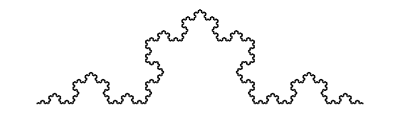

```mathematica
Graphics[{Black,Line[generateCurvePaths[{{-5,0},{5,0}},5,π/3]]}]
```

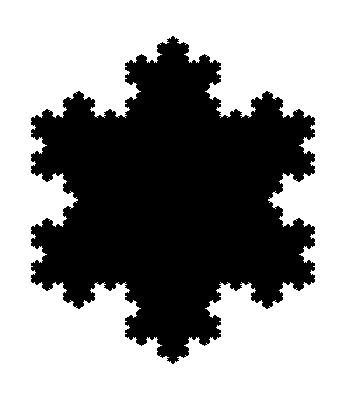

```mathematica
Graphics[{Black,Triangle[equiTriangle],Black,Triangle[generateSnowflakeOverlays[Append[equiTriangle,equiTriangle[[1]]],5,-π/3]]}]
```

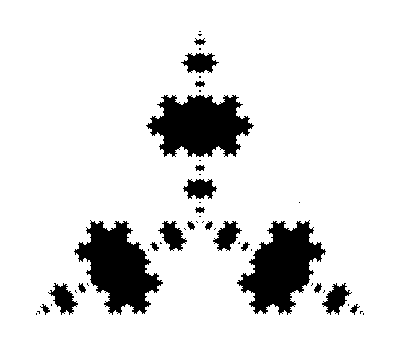

```mathematica
Graphics[{Black,Triangle[equiTriangle],White,Triangle[generateSnowflakeOverlays[Append[equiTriangle,equiTriangle[[1]]],5,π/3]]}]
```

## Cesàro Curve, Snowflake, and Anti-Snowflake (Pure Generation)

```mathematica
cesaroAngle=60;
```

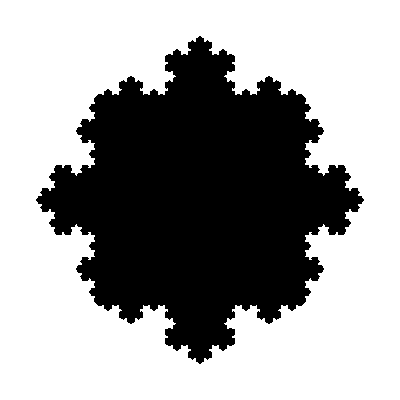

```mathematica
Graphics[{Black,Triangle[square],Black,Triangle[generateSnowflakeOverlays[Append[square,square[[1]]],6,-cesaroAngle π/180]]}]
```

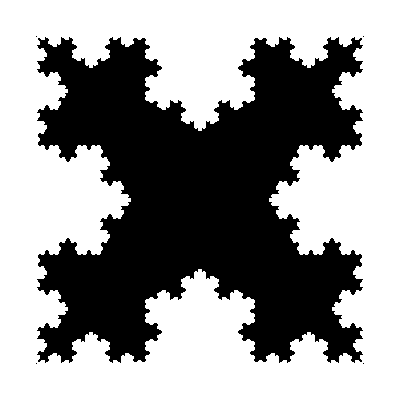

```mathematica
Graphics[{Black,Triangle[square],White,Triangle[generateSnowflakeOverlays[Append[square,square[[1]]],6,cesaroAngle π/180]]}]
```

## Sierpiński Triangle (Pure Generation)

```mathematica
generateOverlays[triangle_,depth_]:=Module[{res,mid},
res={};
If[depth>0,
mid={triangle[[1]]+triangle[[2]],triangle[[2]]+triangle[[3]],triangle[[3]]+triangle[[1]]}/2;
res=Append[res,mid];
res=Join[res,generateOverlays[{triangle[[1]],mid[[1]],mid[[3]]},depth-1]];
res=Join[res,generateOverlays[{triangle[[2]],mid[[1]],mid[[2]]},depth-1]];
res=Join[res,generateOverlays[{triangle[[3]],mid[[2]],mid[[3]]},depth-1]];
];
res
]
```

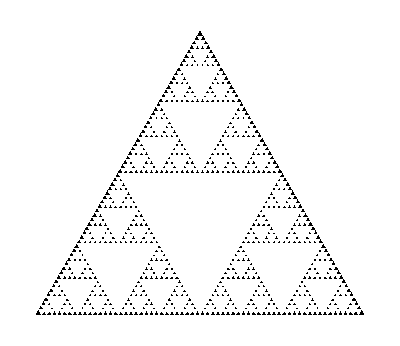

```mathematica
Graphics[{Black,Triangle[equiTriangle],White,Triangle[generateOverlays[equiTriangle,6]]}]
```

## Sierpiński Triangle (Twisted Generation)

```mathematica
generateTwistedOverlays[triangle_,depth_]:=Module[{res,mid},
sides=Append[triangle,triangle[[1]]];
res={};
If[depth≤0,res={triangle},
len=Dimensions[sides][[1]];
mid={};
For[i=1,i<len,i++,
size=sides[[i+1]]-sides[[i]];
size=√(size[[1]]^2+size[[2]]^2);
mid=Append[mid,(sides[[i]]+sides[[i+1]])/2+{RandomReal[amplitude size{-1,1}],RandomReal[amplitude size{-1,1}]}];
];
res=Join[res,generateTwistedOverlays[{triangle[[1]],mid[[1]],mid[[3]]},depth-1]];
res=Join[res,generateTwistedOverlays[{triangle[[2]],mid[[1]],mid[[2]]},depth-1]];
res=Join[res,generateTwistedOverlays[{triangle[[3]],mid[[2]],mid[[3]]},depth-1]];
];
res
]
```

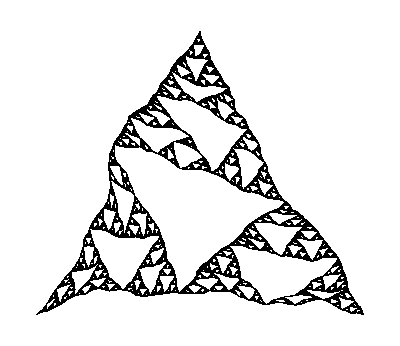

```mathematica
amplitude=0.1;
Graphics[{White,Triangle[equiTriangle],Black,Triangle[generateTwistedOverlays[equiTriangle,6]]}]
```

## Sierpiński Carpet (Pure Generation)

```mathematica
generateCarpetOverlays[square_,depth_]:=Module[{res,mid,d1,d2,c,i,j},
res={};
If[depth>0,
d1=(square[[2]]-square[[1]])/3;
d2=(square[[4]]-square[[1]])/3;
For[i=0,i<3,i++,
For[j=0,j<3,j++,
If[i≠1||j≠1,
c=square[[1]]+i d1+j d2;
res=Join[res,generateCarpetOverlays[{c,c+d1,c+d1+d2,c+d2},depth-1]];
];
];
];
c=square[[1]]+d1+d2;
res=Append[res,{c,c+d1,c+d1+d2,c+d2}];
];
res
]
```

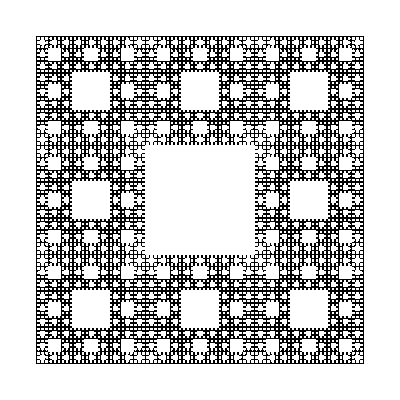

```mathematica
Graphics[{Black,Polygon[square],White,Polygon[generateCarpetOverlays[square,5]]}]
```

## Sierpiński Triangle (Chaos Game Generation)

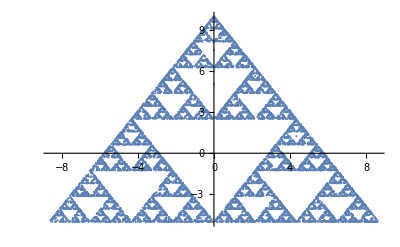

```mathematica
startPoint={0,0};
allpoints={};
For[i=1,i≤10000,i++,
allpoints=Append[allpoints,startPoint];
startPoint=(startPoint+RandomChoice[equiTriangle])/2;
]
ListPlot[allpoints]
```

## Sierpiński Triangle Square Variant (Chaos Game Generation)

0.670764

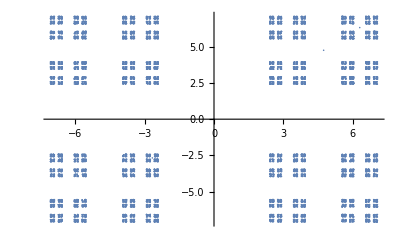

```mathematica
startPoint={0,0};
allpoints={};
rat=RandomReal[]
For[i=1,i≤10000,i++,
allpoints=Append[allpoints,startPoint];
startPoint=(1-rat)startPoint+rat RandomChoice[square];
]
ListPlot[allpoints]
```

## Mandelbrot Sequence

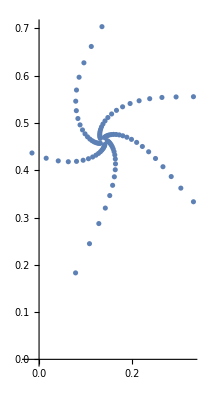

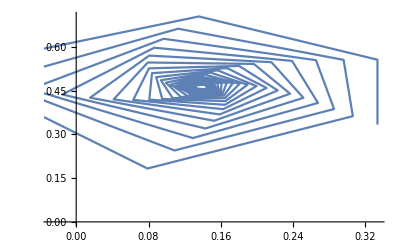

```mathematica
seed=(1+ⅈ)/3;
seq={seed};
curr=seed//N;
For[i=1,i≤100,i++,curr=curr^2+seed;seq=Append[seq,curr]]
coords=Table[{Re[seq[[k]]],Im[seq[[k]]]},{k,Dimensions[seq][[1]]}];
ComplexListPlot[seq]
ListLinePlot[coords]
```

## Mandelbrot Set

```mathematica
mand[curr_,seed_]:=mand[curr,seed]=curr^2+seed
mand2[ind_,seed_]:=mand2[ind,seed]=If[ind>0,If[Abs[mand2[ind-1,seed]]>10^9,∞,mand2[ind-1,seed]^2+seed],seed]
```

```mathematica
check[a_,b_]:=check[a,b]=(
seed=a+b ⅈ;
If[mand2[101,seed]≠∞,Return[Black]];
For[i=1,i≤25,i++,If[mand2[i,seed]==∞,Break[]]];
Return[RGBColor[i/26,0,1-i/26,2/3]];
)
```

```mathematica
set={};
colorList={};
resolution=0.03;
For[a=-2,a≤1,a+=resolution,
For[b=-1.5,b≤1.5,b+=resolution,
set=Append[set,{{a,b}}];
colorList=Append[colorList,check[a,b]];
]
]
```

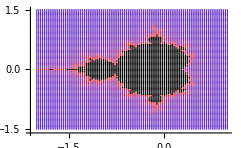

```mathematica
ListPlot[set,PlotStyle->colorList,AxesOrigin->{-2.1,-1.6}]
```

```mathematica
MandelbrotSetPlot[]
```

-Graphics-